# Incorporating an upper bound for J=2: the simplex interior

The conditions 0<c<x≤y≤h restrict (r,s) to lie in the interior volume of a J-dimensional simplex, which is a simple and uniform rescaling of the standard simplex. [There is a reasonably efficient rejection sampling algorithm to sample from this interior volume; see research/paper/sampling_interior_simplex.pdf.]

No analytical solutions for the Lagrange multipliers exist, both for moments <u> and moments <x>. At least for J=2, closed-form expressions for Z, the marginals and <x> exist, but the moment equations cannot be solved analytically. Naieve numerical root finding suffers from scaling problems.

```mathematica
J=n=2;
```

```mathematica
Solve[r==Log[x/c]&&s==Log[y/x]&&0<c<x≤y≤h,{x,y},PositiveReals]//FullSimplify
a={c ⅇ^r,c ⅇ^(r+s) };
b={r,s};
J=Det[Grad[a,b]]//FullSimplify
```

{{x→ConditionalExpression[c ⅇ^r,c>0&&h>c&&0<r<Log[h/c]&&s>0&&r+s≤Log[h/c]],y→ConditionalExpression[c ⅇ^(r+s),c>0&&h>c&&0<r<Log[h/c]&&s>0&&r+s≤Log[h/c]]}}

c^2 ⅇ^(2 r+s)

```mathematica
$Assumptions=0<c<h
bounds={c->200,h->4000}
```

0<c<h

{c→200,h→4000}

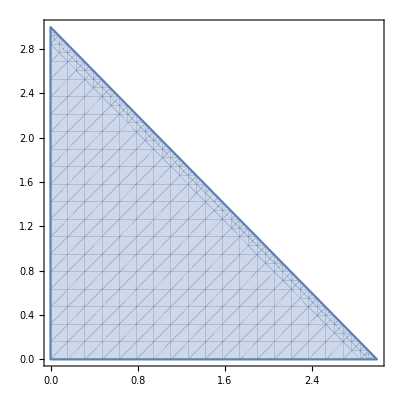

```mathematica
vsimplex = c>0&&h>c&&0<r<Log[h/c]&&s>0&&r+s≤Log[h/c];
RegionPlot[vsimplex/.bounds,{r,0,3},{s,0,3}]
```

```mathematica
m[u_]:=Exp[u.Join[{0},Range[Length[u]-1]//Reverse]] Boole[vsimplex]
m[{r,s}]
```

ⅇ^s Boole[c>0&&h>c&&0<r<Log[h/c]&&s>0&&r+s≤Log[h/c]]

(-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ)))/(c ρ (1+ρ-σ) (-1+σ))

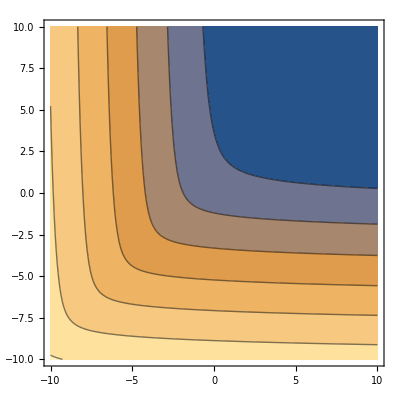

```mathematica
Z[λ_]:=Integrate[m[{r,s}] Exp[-{r,s}.λ],{r,0,∞},{s,0,∞},Assumptions->λ∈Vectors[2,Reals]]//FullSimplify
Z[{ρ,σ}]
ContourPlot[Log[%]/.bounds,{ρ,-10,10},{σ,-10,10}]
```

```mathematica
D[Log[Z[{ρ,σ}]],{{ρ,σ},1}]==-{mr,ms}//FullSimplify
FindRoot[%,{ρ,0},{σ,0}]
```

{mr+1/(-1-ρ+σ)+(c (-1+σ) (1+(c/h)^ρ (-1+ρ Log[c/h])))/(ρ (-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ)))),ms+1/(1+ρ-σ)+(-c ρ+(c/h)^σ h ρ (1+Log[c]-σ Log[c]+(-1+σ) Log[h]))/((-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ))) (-1+σ))}=={0,0}

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{mr+1/(-1-ρ+σ)+(c (-1+σ) (1+(c/h)^ρ (-1+ρ Log[c/h])))/(ρ (-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ)))),ms+1/(1+ρ-σ)+(-c ρ+(c/h)^σ h ρ (1+Log[c]-σ Log[c]+(-1+σ) Log[h]))/((-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ))) (-1+σ))}=={0,0},{ρ,σ}]

```mathematica
p[u_,λ_]:=(1/Z[λ]) m[u] Exp[-u.λ] 
p[{r,s},{ρ,σ}]
```

(c ⅇ^(s-r ρ-s σ) ρ (1+ρ-σ) (-1+σ) Boole[c>0&&h>c&&0<r<Log[h/c]&&s>0&&r+s≤Log[h/c]])/(-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ)))

```mathematica
Integrate[p[{r,s},{ρ,σ}],{r,0,∞},{s,0,∞}]
```

1

## Derive joint distribution and marginals

```mathematica
q[x_,y_,c_,ρ_,σ_]:=p[{Log[x/c],Log[y/x]},{ρ,σ}]/(x y) Boole[0<c≤x≤y≤h]
q[x,y,c,ρ,σ]//FullSimplify
```

Piecewise[{{(c^(1+ρ) x^(-2-ρ+σ) y^-σ ρ (1+ρ-σ) (-1+σ))/(-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ))), r>0&&s>0&&r+s+Log[c]≤Log[h]&&c≤x&&x≤y&&h≥y}, {0, True}}]

```mathematica
q[x_,y_,c_,ρ_,σ_]:=Piecewise[{{(c^(1+ρ) x^(-2-ρ+σ) y^-σ ρ (1+ρ-σ) (-1+σ))/(-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ))), c≤x&&x≤y&&h≥y}, {0, True}}]
```

```mathematica
Integrate[q[x,y,c,ρ,σ],{x,-∞,∞},{y,-∞,∞}]
```

1

```mathematica
px[x_,c_,ρ_,σ_]=Integrate[q[x,y,c,ρ,σ],{y,-∞,∞}]
py[y_,c_,ρ_,σ_]=Integrate[q[x,y,c,ρ,σ],{x,-∞,∞}]
```

Piecewise[{{(c^(1+ρ) h^-σ (1/x)^(2+ρ) (h^σ x-h x^σ) ρ (1+ρ-σ))/(c-c (c/h)^ρ+c ρ-(c/h)^σ h ρ-c σ+c (c/h)^ρ σ), c-h<0&&c-x≤0&&h-x>0}, {0, True}}]

Piecewise[{{-(y^(-1-ρ-σ) (-c^σ y^(1+ρ)+c^(1+ρ) y^σ) ρ (-1+σ))/(c-c (c/h)^ρ+c ρ-(c/h)^σ h ρ-c σ+c (c/h)^ρ σ), c-h<0&&c-y<0&&h-y≥0}, {0, True}}]

```mathematica
px[x,c,-5,2]/.bounds//FullSimplify//N
py[y,c,7,11]/.bounds//FullSimplify//N
```

Piecewise[{{-7.32423×10^-21 (-4000.+x) x^4, 200.≤x<4000.}, {0., True}}]

Piecewise[{{(2.98667×10^17 (-8.×10^6+y^3))/y^11, 200.<y≤4000.}, {0., True}}]

```mathematica
Ex=Integrate[x px[x,c,ρ,σ],{x,-∞,∞}]//FullSimplify
Ey=Integrate[y py[y,c,ρ,σ],{y,-∞,∞}]//FullSimplify
```

(c h^(-ρ-σ) ρ (-c^σ h^(1+ρ) (-1+ρ)+c h^(ρ+σ) (ρ-σ)+c^ρ h^(1+σ) (-1+σ)) (1+ρ-σ))/((-1+ρ) (-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ))) (ρ-σ))

(h^(-ρ-σ) ρ (-1+σ) (c^σ h^(2+ρ) (-1+ρ)+c h^σ (-c^ρ h (-2+σ)+c h^ρ (-1-ρ+σ))))/((-1+ρ) (-c ρ+(c/h)^σ h ρ-c (-1+(c/h)^ρ) (-1+σ)) (-2+σ))

## Solve for Lagrange multipliers given formant frequency first moments

```mathematica
mcond=0<c<mF1<mF2<h;
```

```mathematica
sol=Refine[Solve[mF1==Ex&&mF2==Ey&&mcond,{ρ,σ},Reals],Assumptions->mcond][[1]]//FullSimplify
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

$Aborted

```mathematica
mF={mF1->500,mF2->100};
system = {Ex,Ey}/.bounds/.mF;
sol=FindRoot[system,{ρ,-.00000000001},{σ,.00001}]
```

{ρ→273.042,σ→3.76971}

```mathematica
px[x,c,ρ,σ]/.bounds/.sol//N//FullSimplify
py[y,c,ρ,σ]/.bounds/.sol//N//FullSimplify
```

General::munfl: -3.27538×10^-164 3.54471×10^-190 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.27538×10^-164 3.54471×10^-190 is too small to represent as a normalized machine number; precision may be lost.

Piecewise[{{0., x≥4000.||x<200.}, {(5.18561180251187×10^630)/x^274.042-(5.47207912488194×10^620)/x^271.273, True}}]

General::munfl: -3.27538×10^-164 3.54471×10^-190 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.27538×10^-164 3.54471×10^-190 is too small to represent as a normalized machine number; precision may be lost.

Piecewise[{{0., y>4000.||y≤200.}, {-(5.31412453158021×10^628)/y^274.042+(6.60918×10^6)/y^3.76971, True}}]

## Plots

```mathematica
marginals={Log[px[x,c,ρ,σ]],Log[py[y,c,ρ,σ]]}/.{y->x}/.bounds/.sol//N//FullSimplify
```

General::munfl: -3.27538×10^-164 3.54471×10^-190 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.27538×10^-164 3.54471×10^-190 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.27538×10^-164 3.54471×10^-190 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{Piecewise[{{Log[(5.18561180251187×10^630)/x^274.042-(5.47207912488194×10^620)/x^271.273], 200.≤x<4000.}, {Indeterminate, True}}],Piecewise[{{Log[-(5.31412453158021×10^628)/x^274.042+(6.60918×10^6)/x^3.76971], 200.<x≤4000.}, {Indeterminate, True}}]}

General::munfl: 1/200.1^274.042 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/200.1^271.273 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/200.1^274.042 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^274.042 encountered.

Power::infy: Infinite expression 1/0.^3.76971 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^274.042 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

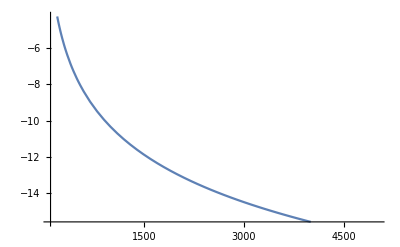

```mathematica
Plot[marginals[[2]],{x,100,5000},PlotRange->Full]
```

```mathematica
Log[(c^(1+ρ) h^-σ (1/x)^(2+ρ) (h^σ x-h x^σ) ρ (1+ρ-σ))/(-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ)))]//Expand
```

Log[(c^(1+ρ) h^-σ (1/x)^(2+ρ) (h^σ x-h x^σ) ρ (1+ρ-σ))/(-(c/h)^σ h ρ+c (ρ+(-1+(c/h)^ρ) (-1+σ)))]